```mathematica
(*Supplementary code for Y. Guo, et.al, arXiv:2502.16567, submitted to ApJ.
To solve Eqs. 26 and 27 for the uniform case.
Run on Wolfram Mathematica 14.0.

We'll demonstrate how to reproduce Fig. 3 in our article. Reproduction of Figs. 1 and 2 can be done by a similar approach.

This code has not been optimized and it may takes 2 hours for one's pc to obtain a result.
*)
```

```mathematica
ClearAll["Global`*"];
```

```mathematica
(*Normalizing the basic parameters Subscript[ω, p] and c.*)
wp=1;c=1;
```

```mathematica
(*Reference dispersion relation in absence of the external magnetic field, see Gruzinov 2008.*)
w0[kV_]:=Sqrt[wp^2/2*(Sqrt[1+8*kV^2/wp^2]-1-2*kV^2/wp^2)];
```

```mathematica
(*Defining the coefficients in the eigenvalue equations.*)
Omega[V_]:=w-k*V;
Arel[V_]:=(w-k*V)^2*(w^2-k^2*c^2-wp^2*gam[V]^2)-wc^2*(w^2-k^2*c^2);
Brel[V_]:=1/c^2*((w-k*V)^2*(w^2-k^2*c^2-wp^2*gam[V]^2)^2-wc^2*(w^2-k^2*c^2)^2);
gam[V_]:=1/Sqrt[1-V^2/c^2];
```

```mathematica
(*Solving the dispersion relation, following the Appendix.
grel for uniform magnetic fields and
frel for anti-parallel magnetic fields.
The function gives a complex frequency with a largest imaginary part, corresponding to

B0=Subscript[ω, c]/Subscript[ω, p], 
	k1=k*Subscript[V, 0]/Subscript[ω, p],
    and V0 is normalized by c=1.
*)

grel[B0_,k1_,V0_]:=(wc=wp*B0;k=k1*wp/V0;(w/.NSolve[{w*(wc^2+wp^2-Omega[V0]^2)*(a1^2*A1)+w/c^2(wp^2/Omega[V0]^2-1)*Arel[V0]*A1-(wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)*a1*C1==0,
w*(wc^2+wp^2-Omega[V0]^2)*(b1^2*B1)+w/c^2(wp^2/Omega[V0]^2-1)*Arel[V0]*B1-(wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)*b1*D1==0,w*(wc^2+wp^2-Omega[-V0]^2)*(a2^2*A2)+w/c^2(wp^2/Omega[-V0]^2-1)*Arel[-V0]*A2-(wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)*a2*C2==0,
w*(wc^2+wp^2-Omega[-V0]^2)*(b2^2*B2)+w/c^2(wp^2/Omega[-V0]^2-1)*Arel[-V0]*B2-(wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)*b2*D2==0,
Arel[V0]*(a1^2*C1)+Brel[V0]*C1-(w*wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)*a1*A1==0,
Arel[V0]*(b1^2*D1)+Brel[V0]*D1-(w*wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)*b1*B1==0,
Arel[-V0]*(a2^2*C2)+Brel[-V0]*C2-(w*wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)*a2*A2==0,
Arel[-V0]*(b2^2*D2)+Brel[-V0]*D2-(w*wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)*b2*B2==0,
A1+B1==1,A2+B2==1,C1+D1==C2+D2,a1*C1+b1*D1==a2*C2+b2*D2,
w/Arel[V0]*(wc^2+wp^2-Omega[V0]^2)*(a1*A1+b1*B1)-(wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)/Arel[V0]*(C1+D1)==
w/Arel[-V0]*(wc^2+wp^2-Omega[-V0]^2)*(a2*A2+b2*B2)-(wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)/Arel[-V0]*(C2+D2),Re[a1]<0,Re[b1]<0,Re[a2]>0,Re[b2]>0,Im[w]>0,Re[w]<=0}])//Union) /.{Union[w]->0}//First[MaximalBy[#,Abs@*Im]]&
```

```mathematica
frel[B0_,k1_,V0_]:=(wc=wp*B0;k=k1*wp/V0;(w/.NSolve[{w*(wc^2+wp^2-Omega[V0]^2)*(a1^2*A1)+w/c^2(wp^2/Omega[V0]^2-1)*Arel[V0]*A1-(wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)*a1*C1==0,
w*(wc^2+wp^2-Omega[V0]^2)*(b1^2*B1)+w/c^2(wp^2/Omega[V0]^2-1)*Arel[V0]*B1-(wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)*b1*D1==0,w*(wc^2+wp^2-Omega[-V0]^2)*(a2^2*A2)+w/c^2(wp^2/Omega[-V0]^2-1)*Arel[-V0]*A2-(-wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)*a2*C2==0,
w*(wc^2+wp^2-Omega[-V0]^2)*(b2^2*B2)+w/c^2(wp^2/Omega[-V0]^2-1)*Arel[-V0]*B2-(-wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)*b2*D2==0,
Arel[V0]*(a1^2*C1)+Brel[V0]*C1-(w*wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)*a1*A1==0,
Arel[V0]*(b1^2*D1)+Brel[V0]*D1-(w*wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)*b1*B1==0,
Arel[-V0]*(a2^2*C2)+Brel[-V0]*C2-(w*-wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)*a2*A2==0,
Arel[-V0]*(b2^2*D2)+Brel[-V0]*D2-(w*-wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)*b2*B2==0,
A1+B1==1,A2+B2==1,C1+D1==C2+D2,a1*C1+b1*D1==a2*C2+b2*D2,
w/Arel[V0]*(wc^2+wp^2-Omega[V0]^2)*(a1*A1+b1*B1)-(wc*wp^2*gam[V0]^2)*(k-w*V0/c^2)/Arel[V0]*(C1+D1)==
w/Arel[-V0]*(wc^2+wp^2-Omega[-V0]^2)*(a2*A2+b2*B2)-(-wc*wp^2*gam[V0]^2)*(k+w*V0/c^2)/Arel[-V0]*(C2+D2),Re[a1]<0,Re[b1]<0,Re[a2]>0,Re[b2]>0,Im[w]>0,Re[w]<=0}])//Union) /.{Union[w]->0}//First[MaximalBy[#,Abs@*Im]]&
```

```mathematica
(*Generating the table for Subscript[ω, c]=0.6 Subscript[ω, p], Subscript[V, 0]=0.2c, for example.
ParallelTable can be used for multi cores.
For a single core, use Table instead.
*)
rel02=ParallelTable[grel[3/5,l,2/10],{l,0,12/10,24 (*This parameter controls the calculation points.*)}];
```

```mathematica
rel099=ParallelTable[grel[3/5,l,99/100],{l,0,12/10,24}];
rel06=ParallelTable[grel[3/5,l,6/10],{l,0,12/10,24}];
rel03=ParallelTable[grel[3/5,l,3/10],{l,0,12/10,24}];
rel001=ParallelTable[grel[3/5,l,1/100],{l,0,12/10,24}];
```

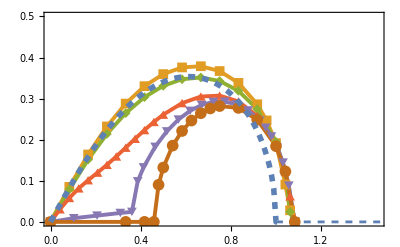

```mathematica
(*Generate Fig. 3 in our article. Figs. 1 and 2 can be generated by fixing V0 but varying B0 in the functions above.*)
figv=Show[{ListLinePlot[{{0,0},{Re[#1],Im[#2]}&@@@rel099,{Re[#1],Im[#2]}&@@@rel06,{Re[#1],Im[#2]}&@@@rel03,{Re[#1],Im[#2]}&@@@rel02,{Re[#1],Im[#2]}&@@@rel001},Frame->True,FrameStyle->Directive[Black,AbsoluteThickness[1.5]],PlotRange->{{0,1.45},{0,0.5}},PlotMarkers->{None,{Automatic,10},{Automatic,10},{Automatic,10},{Automatic,10},{Style["●",12],12},{Style["★",12],12}},PlotLegends->Placed[LineLegend[{Style["",FontSize->14],Style["",FontSize->14],Style["",FontSize->14],Style["",FontSize->14],Style["",FontSize->14],Style["",FontSize->14]},"Spacings"->-0.1,LegendMarkerSize->{20,13}],{0.84,0.73}],PlotStyle->{Dashed,Thickness[0.007],Thickness[0.007],Thickness[0.007],Thickness[0.007],Thickness[0.007]},FrameLabel->{Style["",Black,FontSize->15],Style["",Black,FontSize->15]},FrameTicksStyle->Directive[Black,16],Epilog->{Text[Style[Framed[""],FontSize->14],{0.24,0.44}]}],Plot[w0[x],{x,0,1.2},PlotStyle->{Dashed,Thickness[0.01]}]}]
```